Make a movie showing the result of pushing a normally distributed swarm of robots into a wall

```mathematica
n = 10^2;(*number of robots*)
friction[b_,input_,dist_]:=If[input⟦1⟧>b,{b,input⟦2⟧-dist},input]
truncateXTob[b_,input_]:=If[input⟦1⟧>b,{b,input⟦2⟧},input]
truncateXTonb[b_,input_]:=If[input⟦1⟧<b,{b,input⟦2⟧},input]
truncateYToa[a_,input_]:=If[input⟦2⟧>a,{input⟦1⟧,a},input]
pts = RandomVariate[BinormalDistribution[{0,0},{1,1},0],n];
```

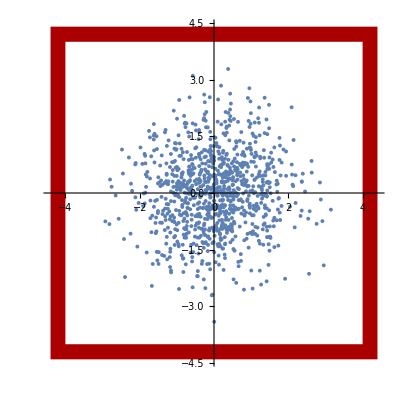

```mathematica
L = 4;
plotr =(1.1 L){{-1,1},{-1,1}};
ListPlot[pts,PlotRange->plotr, AspectRatio->1,Prolog->{Darker[Red],Rectangle[1.1L{-1,-1},1.1L{1,1}],White,Rectangle[L{-1,-1},L{1,1}]}]
```

### TODO : make the rectangle 2w and 1 h stop pts on boundary draw the mean and 95% confidence ellipse of the robots. draw the initial mean and 95% confidence ellipse of the robots. Make a separate version that shows the effects of friction.

```mathematica
(1.1 L){{-1,1},{-2,2}}
```

{{-4.4,4.4},{-8.8,8.8}}

```mathematica
L = 4;
bwid = 1/10; (*border width*)
plotr = L{{-2-bwid,2+bwid},{-1-bwid,1+bwid}};
Manipulate[Module[{pos=Map[{x,y}+#&,pts]},

ListPlot[{Select[pos,#⟦1⟧<2L&] }

,PlotRange->plotr, AspectRatio->1/2,Prolog->{Darker[Red],Rectangle[L{-2-bwid,-1-bwid},L{2+bwid,1+bwid}],White,Rectangle[L{-2,-1},L{2,1}]}]],{{x,0},-10,10,Appearance-> Labeled},{{y,0},-4,4,Appearance-> Labeled}]
```

```mathematica
aba
b
p = {{1,2},{1,9},{1,10}}
Cases[p,{aba_,bab_}->{aba,Min[bab,5]}]
```

aba

1/3

{{1,2},{1,9},{1,10}}

{{1,2},{1,5},{1,5}}

```mathematica
limX[{-50,10}]
f[{-50,10}]
```

-8

{-49,11}

```mathematica
(*what is the fastest way?*)
n=2000;
pts = RandomVariate[BinormalDistribution[{0,0},{1,1},0],n];

Timing[{Clip[#1,{-2L,2L}],Clip[#1,{-L,L}]}&@@@trialList;]
Timing[Transpose[{Clip[#1,{-2L,2L}],Clip[#1,{-L,L}]}&@@Transpose[pts]];]
Timing[Transpose[{Thread[Clip[#1,{-2L,2L}]],Thread[Clip[#1,{-L,L}]]}&@@Transpose[pts]];]
```

{0.00523,Null}

{0.00005,Null}

{0.00031,Null}

```mathematica
L = 4;
bwid = 1/10; (*border width*)
limX[x_]:=Max[Min[x,2L],-2L];
limY[x_]:=Max[Min[x,2L],-2L];
plotr = L{{-2-2bwid,2+2bwid},{-1-2bwid,1+2bwid}};
Manipulate[Module[{pos=Map[{x,y}+#&,pts],Clipped, mean, cov},
Clipped=Transpose[{Clip[#1,{-2L,2L}],Clip[#2,{-L,L}]}&@@Transpose[pos]];
cov =Covariance[Clipped]; 
mean = Mean[Clipped];
ListPlot[Clipped

,PlotRange->plotr, AspectRatio->1/2,Prolog->{Darker[Red],Rectangle[L{-2-bwid,-1-bwid},L{2+bwid,1+bwid}],White,Rectangle[L{-2,-1},L{2,1}]},
Epilog->{Opacity[0],EdgeForm[{Thick,Red}],Ellipsoid[mean,6 cov]}

]],{{x,0},-10,10,Appearance-> Labeled},{{y,0},-5,5,Appearance-> Labeled},
{{Δx,0},{-1,1},Appearance-> Labeled},{{Δy,0},{"-1","1"}}
,{friction,{False,True}}]
```

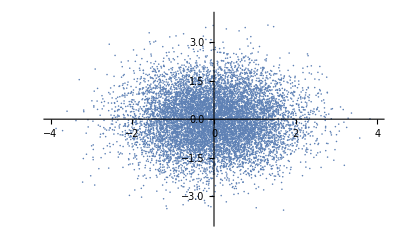

Covariance of data is 1.00896 | 0.00170027
0.00170027 | 1.01373.

Covariance of data is 0.486832 | 0.00345638
0.00345638 | 1.01373, when x_max=1/3

Covariance of data is 0.486832 | 0.00377915
0.00377915 | 0.561509, when x_max=1/3,y_max=1/2

Thread::tdlen: Objects of unequal length in {{1/3, -0.410331}, {-0.173746, 0.0355677}, {1/3, -0.0204442}, {0.12792, 1.01883}, {-2.24917, 0.905697}, {1/3, -2.19015}, {-0.122198, -2.42046}, {1/3, 0.158876}, « 35 », {-1.17618, 0.663266}, {1/3, 0.0692706}, {1/3, -0.435129}, {-0.59407, 0.27461}, {0.271376, -0.0498082}, {1/3, 1.63752}, {1/3, 0.695769}, « 9950 »} + {{« 20 », « 18 »}, « 49 », « 950 »} cannot be combined.

Covariance::arg1: The first argument must be either a vector, a matrix, or a multivariate distribution.

Covariance[{{0.0815921,0.996354},{-0.625254,-1.63884},{1.42874,-0.649271},{2.13756,0.812708},{0.0255642,1.20748},{0.439167,0.729632},989,{-0.912737,-0.119483},{1.2259,0.888922},{-0.381284,0.753757},{0.0369321,-0.992604},{-1.55337,0.460604}}+{1}]
 |  |  |  |

Covariance::arg1: The first argument must be either a vector, a matrix, or a multivariate distribution.

Covariance[If[{0.0815921,0.996354}>1/3,{1/3,1},{{0.0815921,0.996354},{-0.625254,-1.63884},{1.42874,-0.649271},{2.13756,0.812708},{0.0255642,1.20748},990,{-0.912737,-0.119483},{1.2259,0.888922},{-0.381284,0.753757},{0.0369321,-0.992604},{-1.55337,0.460604}}]+If[1]]
 |  |  |  |

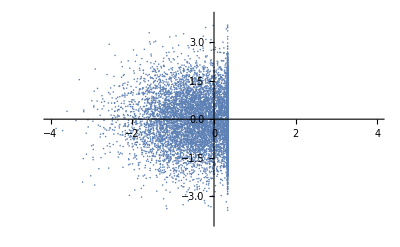

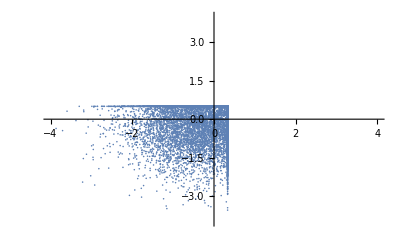

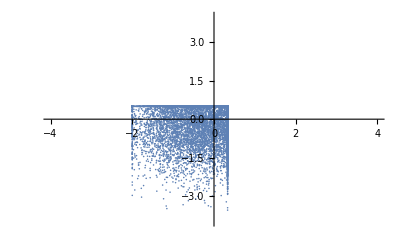

Covariance of data is 0.447019 | 0.00340236
0.00340236 | 0.561509, when x limited to=[-2,1/3,y_max=1/2

```mathematica
n = 10^3;(*number of robots*)
plotr = 2*{{-2,2},{-2,2}};
ListPlot[pts,PlotRange->plotr]
b = 1/3;
a = 1/2;
bmin = -2;
ptsx =Map[truncateXTob[b,#]&,pts];
(*ptsx =Map[truncateXTonb[-1,#]&,pts];*)
ptsab =Map[truncateYToa[a,#]&,ptsx];
StringForm["Covariance of data is ``.",Covariance[pts]//MatrixForm]
StringForm["Covariance of data is ``, when x_max=``",Covariance[ptsx]//MatrixForm,b]
StringForm["Covariance of data is ``, when x_max=``,y_max=``",Covariance[ptsab]//MatrixForm,b,a]
ptsxM =ptsx+RandomVariate[BinormalDistribution[{0,0},{1,1},0],n];
ptsBothSifes =Map[ truncateXTonb[bmin,#]&,ptsab];
Covariance[ptsxM]//MatrixForm
ptsxMx =Map[truncateXTob[b,#]&,ptsxM];
Covariance[ptsxMx]//MatrixForm
ListPlot[ptsx,PlotRange->plotr]
ListPlot[ptsab,PlotRange->plotr]
ListPlot[ptsBothSifes,PlotRange->plotr]
StringForm["Covariance of data is ``, when x limited to=[``,``,y_max=``",Covariance[ptsBothSifes]//MatrixForm,bmin,b,a]
```

### What happens to mean and variance if all the robots past x=b are pushed horizontally back to b? Trying MonteCarlo Analysis Things for Shiva to try: Change the function truncateXTob[b_,input_], to add friction that pulls each particle that hits a wall in the y-direction

```mathematica
{{Subscript[σ, 1]^2,ρ Subscript[σ, 1] Subscript[σ, 2]},{ρ Subscript[σ, 1] Subscript[σ, 2],Subscript[σ, 2]^2}}//MatrixForm (*definition of covariance matrix*)
```

(σ_1^2 | ρ σ_1 σ_2
ρ σ_1 σ_2 | σ_2^2)

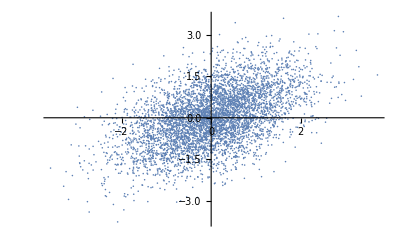

```mathematica
out = RandomVariate[BinormalDistribution[1/2],5000];
ListPlot[out]
```

BinormalDistribution[{μ1, μ2}, {σ1, σ2}, ρ]
represents a bivariate normal distribution with mean {μ_1, μ_2} and covariance matrix {{σ_1^2,ρ σ_1 σ_2},{ρ σ_1 σ_2,σ_2^2}}.

```mathematica
n = 10^4;
plotr = 2*{{-2,2},{-2,2}};
pts = RandomVariate[BinormalDistribution[{0,0},{1,1},0],n];
ListPlot[pts,PlotRange->plotr]
b = 1/3;
a = 1/2;
bmin = -2;
ptsx =Map[truncateXTob[b,#]&,pts];
(*ptsx =Map[truncateXTonb[-1,#]&,pts];*)
ptsab =Map[truncateYToa[a,#]&,ptsx];
StringForm["Covariance of data is ``.",Covariance[pts]//MatrixForm]
StringForm["Covariance of data is ``, when x_max=``",Covariance[ptsx]//MatrixForm,b]
StringForm["Covariance of data is ``, when x_max=``,y_max=``",Covariance[ptsab]//MatrixForm,b,a]
ptsxM =ptsx+RandomVariate[BinormalDistribution[{0,0},{1,1},0],n];
ptsBothSifes =Map[ truncateXTonb[bmin,#]&,ptsab];
Covariance[ptsxM]//MatrixForm
ptsxMx =Map[truncateXTob[b,#]&,ptsxM];
Covariance[ptsxMx]//MatrixForm
ListPlot[ptsx,PlotRange->plotr]
ListPlot[ptsab,PlotRange->plotr]
ListPlot[ptsBothSifes,PlotRange->plotr]
StringForm["Covariance of data is ``, when x limited to=[``,``,y_max=``",Covariance[ptsBothSifes]//MatrixForm,bmin,b,a]
```

-Graphics-

Covariance of data is 1.00896 | 0.00170027
0.00170027 | 1.01373.

$Aborted

$Aborted

$Aborted

«5 more identical outputs»

#### What happens to mean and variance if all the robots past x=b are pushed horizontally back to b? I found an equation for the mean and for the variance. What is the definition of the correlation constant ρ?

```mathematica
PDF[MultinormalDistribution[{Subscript[μ, x],Subscript[μ, y]},({{Subscript[σ, x]^2, ρ Subscript[σ, x] Subscript[σ, y]}, {ρ Subscript[σ, x] Subscript[σ, y], Subscript[σ, y]^2}})],{x,y}]
```

(ⅇ^(1/2 (-((x-μ_x) (y ρ σ_x-ρ μ_y σ_x-x σ_y+μ_x σ_y))/((-1+ρ^2) σ_x^2 σ_y)-((y-μ_y) (-y σ_x+μ_y σ_x+x ρ σ_y-ρ μ_x σ_y))/((-1+ρ^2) σ_x σ_y^2))))/(2 π √(σ_x^2 σ_y^2-ρ^2 σ_x^2 σ_y^2))

```mathematica
∫_b^∞ (ⅇ^(1/2 (-((x-Subscript[μ, x]) (y ρ Subscript[σ, x]-ρ Subscript[μ, y] Subscript[σ, x]-x Subscript[σ, y]+Subscript[μ, x] Subscript[σ, y]))/((-1+ρ^2) Subscript[σ, x]^2 Subscript[σ, y])-((y-Subscript[μ, y]) (-y Subscript[σ, x]+Subscript[μ, y] Subscript[σ, x]+x ρ Subscript[σ, y]-ρ Subscript[μ, x] Subscript[σ, y]))/((-1+ρ^2) Subscript[σ, x] Subscript[σ, y]^2))))/(2 π √(Subscript[σ, x]^2 Subscript[σ, y]^2-ρ^2 Subscript[σ, x]^2 Subscript[σ, y]^2))ⅆx
```

∫_b^∞ (ⅇ^(1/2 (-((x-μ_x) (y ρ σ_x-ρ μ_y σ_x-x σ_y+μ_x σ_y))/((-1+ρ^2) σ_x^2 σ_y)-((y-μ_y) (-y σ_x+μ_y σ_x+x ρ σ_y-ρ μ_x σ_y))/((-1+ρ^2) σ_x σ_y^2))))/(2 π √(σ_x^2 σ_y^2-ρ^2 σ_x^2 σ_y^2))ⅆx

```mathematica
PDF[MultinormalDistribution[{Subscript[μ, x],Subscript[μ, y]},({{Subscript[σ, x]^2, 0}, {0, Subscript[σ, y]^2}})],{x,y}]
```

(ⅇ^(1/2 (-(x-μ_x)^2/σ_x^2-(y-μ_y)^2/σ_y^2)))/(2 π √(σ_x^2 σ_y^2))

```mathematica
(ⅇ^(1/2 (-(x-Subscript[μ, x])^2/Subscript[σ, x]^2-(y-Subscript[μ, y])^2/Subscript[σ, y]^2)))/(2 π √(Subscript[σ, x]^2 Subscript[σ, y]^2))
```

```mathematica
PDF[NormalDistribution[Subscript[μ, x],Subscript[σ, x]],{x}]
```

{(ⅇ^(-(x-μ_x)^2/(2 σ_x^2)))/(√(2 π) σ_x)}

```mathematica
(ⅇ^(-(x-Subscript[μ, x])^2/(2 Subscript[σ, x]^2)))/(√(2 π) Subscript[σ, x])
```

```mathematica
∫_b^∞ (ⅇ^(-x^2/2))/(√(2 π))ⅆx
```

1/2 Erfc[b/(√2)]

```mathematica
PDF[MultinormalDistribution[{0,0},({{Subscript[σ, x]^2, 0}, {0, Subscript[σ, y]^2}})],{x,y}]
```

(ⅇ^(1/2 (-x^2/σ_x^2-y^2/σ_y^2)))/(2 π √(σ_x^2 σ_y^2))

```mathematica
𝒟=ProbabilityDistribution[Piecewise[{{(ⅇ^(-x^2/2))/(√(2 π)), x<b}, {1/2 Erfc[b/(√2)], x==b}, {0, True}}],{x,-∞,∞}];
```

```mathematica
PDF[𝒟,x]
```

Piecewise[{{(ⅇ^(-x^2/2))/(√(2 π)), -b+x<0}, {1/2 Erfc[b/(√2)], -b+x==0}, {0, True}}]

```mathematica
-(ⅇ^(-b^2/2))/(√(2 π))
```

```mathematica
MeanX [b_]:=∫_(-∞)^b x(ⅇ^(-x^2/2))/(√(2 π))ⅆx+b 1/2 Erfc[b/(√2)]
MeanFunc[b_]:=-(ⅇ^(-b^2/2))/(√(2 π))+1/2 b Erfc[b/(√2)](*the solution*)
VarX [b_]:=∫_(-∞)^b x^2(ⅇ^(-x^2/2))/(√(2 π))ⅆx+b 1/2 Erfc[b/(√2)]-MeanFunc[b]^2
VarXFunc[b_]:=1/2 (1-b ⅇ^(-b^2/2) √(2/π)+Erf[b/(√2)]+b Erfc[b/(√2)]-2 ((ⅇ^(-b^2/2))/(√(2 π))-1/2 b Erfc[b/(√2)])^2)
```

```mathematica
meanV =-(ⅇ^(-b^2/2))/(√(2 π))/.{b->1};
PDF[𝒟,x]/.{b->1};

Manipulate[Plot[Piecewise[{{(ⅇ^(-x^2/2))/(√(2 π)), x<b}, {1/2 Erfc[b/(√2)], x==b}, {0, True}}],{x,-4,4},Filling->Axis,Epilog->{
 PointSize[Large],Blue,Line[{{b,0},{b,1/2 Erfc[b/(√2)]}}],Point[{b,1/2 Erfc[b/(√2)]}],
Red,Point[{MeanFunc[b],0}]},PlotRange->{{-4,4},{-.05,1}}],{b,-4,4}]
```

```mathematica
Mean[𝒟]
```

-(ⅇ^(-b^2/2))/(√(2 π))

```mathematica
MeanFunc[b]
```

-(ⅇ^(-b^2/2))/(√(2 π))+1/2 b Erfc[b/(√2)]

```mathematica
Manipulate[Plot[Sin[f x+u],{x,0,2π}],{u, 0 , 2π}, {f, 1,10}]
```